```mathematica
pic=ImageData[-Graphics-]⟦All,All,1⟧;
```

```mathematica
dir={{0,1},{1,0},{0,-1},{-1,0}};(*This loop searches for the first edge to work around*)For[x=2;s={};xs=0;ys=0;n=0,x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0&&Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0,
xs=x;ys=y;x=480;y=640;s=Append[s,{xs,ys,pic⟦xs,ys⟧}]]]];
{xs,ys}
(*we consider 4 different directions, we always try to turn left if possible, think working through a maze with left hand on a wall*)
If[pic⟦xs+dir⟦1,1⟧,ys+dir⟦1,2⟧⟧≠0,xc=xs+dir⟦1,1⟧;yc=ys+dir⟦1,2⟧;ds=1;d=1,If[pic⟦xs+dir⟦2,1⟧,ys+dir⟦2,2⟧⟧≠0,xc=xs+dir⟦2,1⟧;yc=ys+dir⟦2,2⟧;ds=2;d=2]];
While[xc≠ xs||yc≠ ys,s=Append[s,{xc,yc ,pic⟦xc,yc⟧}];  If[pic⟦xc+dir⟦Mod[d-1,4,1],1⟧,yc+dir⟦Mod[d-1,4,1],2⟧⟧≠0,xc=xc+dir⟦Mod[d-1,4,1],1⟧;yc=yc+dir⟦Mod[d-1,4,1],2⟧;d=Mod[d-1,4,1],
If[pic⟦xc+dir⟦Mod[d,4,1],1⟧,yc+dir⟦Mod[d,4,1],2⟧⟧≠0,xc=xc+dir⟦Mod[d,4,1],1⟧;yc=yc+dir⟦Mod[d,4,1],2⟧;d=Mod[d,4,1],
If[pic⟦xc+dir⟦Mod[d+1,4,1],1⟧,yc+dir⟦Mod[d+1,4,1],2⟧⟧≠0,xc=xc+dir⟦Mod[d+1,4,1],1⟧;yc=yc+dir⟦Mod[d+1,4,1],2⟧;d=Mod[d+1,4,1],
If[pic⟦xc+dir⟦Mod[d+2,4,1],1⟧,yc+dir⟦Mod[d+2,4,1],2⟧⟧≠0,xc=xc+dir⟦Mod[d+2,4,1],1⟧;yc=yc+dir⟦Mod[d+2,4,1],2⟧;d=Mod[d+2,4,1]]]]]]
```

{33,305}

```mathematica
len=Length[s]//N;
```

```mathematica
jmax=15;dat=Table[(2 If[j==0,0.5,1])/len Sum[KroneckerProduct[{Sin[(2π j X)/len],Cos[(2π j X)/len]},s⟦X⟧],{X,1,len}],{j,0,jmax}];
Sum[%⟦j,1⟧ Sin[2π (j-1) X]+%⟦j,2⟧ Cos[2π(j-1) X],{j,1,jmax+1}];
Show[ListPointPlot3D[Table[%,{X,0,1,1/200}],PlotStyle->Red],ListPointPlot3D[s]]
```

-Graphics3D-

```mathematica
Sum[dat⟦j,1⟧ Sin[2π (j-1) X]+dat⟦j,2⟧ Cos[2π(j-1) X],{j,1,jmax+1}];
FindRoot[%⟦1⟧==200,{X,5}]
```

{235.263-183.36 Cos[2 π X]+22.5252 Cos[4 π X]-0.508439 Cos[6 π X]-11.9779 Cos[8 π X]-5.04021 Cos[10 π X]-5.62772 Cos[12 π X]-3.4587 Cos[14 π X]-7.54651 Cos[16 π X]-2.4441 Cos[18 π X]-1.44533 Cos[20 π X]+0.0306344 Cos[22 π X]+2.81486 Cos[24 π X]+0.385307 Cos[26 π X]-1.58238 Cos[28 π X]-1.37532 Cos[30 π X]+12.0315 Sin[2 π X]+22.846 Sin[4 π X]+8.31885 Sin[6 π X]-10.3207 Sin[8 π X]-10.4761 Sin[10 π X]-2.72377 Sin[12 π X]+1.35375 Sin[14 π X]+4.77962 Sin[16 π X]+3.89443 Sin[18 π X]+1.43899 Sin[20 π X]+0.127008 Sin[22 π X]-2.36152 Sin[24 π X]-1.96932 Sin[26 π X]-2.14987 Sin[28 π X]-0.947152 Sin[30 π X],281.275-43.8925 Cos[2 π X]+18.8213 Cos[4 π X]+36.7306 Cos[6 π X]+6.56629 Cos[8 π X]+10.554 Cos[10 π X]+1.93524 Cos[12 π X]-4.83654 Cos[14 π X]+4.26245 Cos[16 π X]-4.62945 Cos[18 π X]-0.271352 Cos[20 π X]+3.03714 Cos[22 π X]-2.83636 Cos[24 π X]+0.645341 Cos[26 π X]-1.38243 Cos[28 π X]-1.17559 Cos[30 π X]+146.322 Sin[2 π X]-59.8309 Sin[4 π X]+6.13819 Sin[6 π X]-1.0357 Sin[8 π X]+17.2342 Sin[10 π X]+6.38665 Sin[12 π X]+3.92457 Sin[14 π X]+2.67669 Sin[16 π X]-1.85727 Sin[18 π X]+1.99913 Sin[20 π X]-2.27749 Sin[22 π X]-0.026776 Sin[24 π X]-0.093639 Sin[26 π X]+1.21213 Sin[28 π X]+2.64912 Sin[30 π X],0.452208-0.029262 Cos[2 π X]-0.0591576 Cos[4 π X]+0.019769 Cos[6 π X]+0.0131431 Cos[8 π X]+0.0195686 Cos[10 π X]-0.0212159 Cos[12 π X]-0.0196701 Cos[14 π X]-0.0264224 Cos[16 π X]-0.00221578 Cos[18 π X]-0.00655767 Cos[20 π X]+0.012898 Cos[22 π X]-0.000500876 Cos[24 π X]+0.00482531 Cos[26 π X]+0.000319443 Cos[28 π X]+0.00982681 Cos[30 π X]+0.0441394 Sin[2 π X]+0.0426533 Sin[4 π X]+0.0207919 Sin[6 π X]-0.0200216 Sin[8 π X]-0.0314019 Sin[10 π X]-0.0342203 Sin[12 π X]-0.0126359 Sin[14 π X]+0.00445655 Sin[16 π X]+0.00919803 Sin[18 π X]+0.00952088 Sin[20 π X]-0.000182109 Sin[22 π X]-0.0034988 Sin[24 π X]-0.00161198 Sin[26 π X]-0.00420396 Sin[28 π X]-0.00254676 Sin[30 π X]}

{X→4.1668}

{}

```mathematica
Solve[{ya==α xa+β,yb==α xb+β},{α,β}]⟦1⟧
Simplify[(α X+β)/.%]
```

{α→-(-ya+yb)/(xa-xb),β→-(xb ya-xa yb)/(xa-xb)}

(X ya-xb ya-X yb+xa yb)/(xa-xb)

```mathematica
s⟦1⟧
```

{33,305,0.360784}

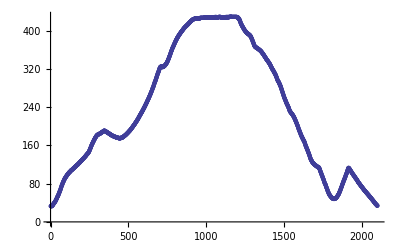

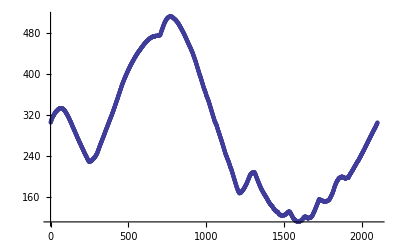

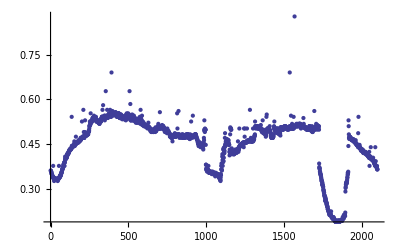

```mathematica
ListPlot[s⟦All,1⟧]
ListPlot[s⟦All,2⟧]
(*This is the depth information*)
ListPlot[s⟦All,3⟧]
```

```mathematica
ListPointPlot3D[Table[{s⟦i,1⟧,s⟦i,2⟧,s⟦i,3⟧},{i,1,Length[s]}]]
```

-Graphics3D-